# Systems of Differential Equations

Considering a system of differential equations of the form:
ẋ = 1/2(x-x^3) - y-1/2 x y^2
ẏ = x -1/2 x^2 y+ 1/2 y - 1/2 y^3

## Define the functions

```mathematica
f = 1/2 x - y - 1/2(x^3+x y^2);
g = x + 1/2 y - 1/2(y^3+x^2 y);
```

## Step 1: Find the “Easy” Solutions (Equilibrium Points)

```mathematica
eqPts = Solve[{f==0,g==0},{x,y}]
```

{{x→0,y→0}}

## Step 2: Linearize about the Equilibrium Points

Let’s first determine the Jacobian.

```mathematica
Df = {{D[f,x],D[f,y]},{D[g,x],D[g,y]}};
Df//MatrixForm
```

(1/2+1/2 (-3 x^2-y^2) | -1-x y
1-x y | 1/2+1/2 (-x^2-3 y^2))

### The Linearization at (x^*,y^*)→(0,0)

```mathematica
J = Df/.eqPts[[1]];
J//MatrixForm
```

(1/2 | -1
1 | 1/2)

{{1/2+ⅈ,1/2-ⅈ},{{ⅈ,1},{-ⅈ,1}}}

{1/2+ⅈ,1/2-ⅈ}

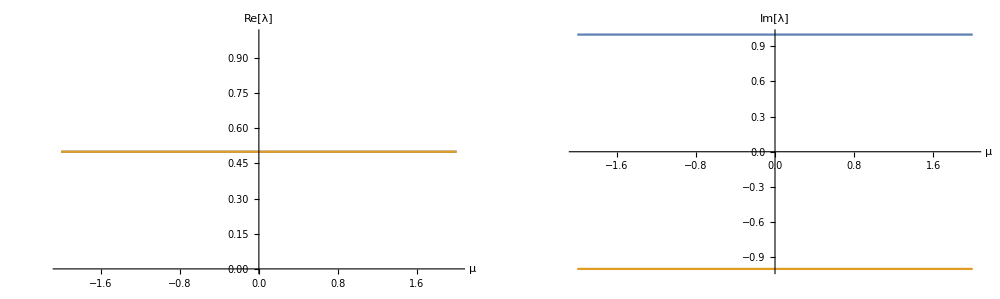

```mathematica
esys1 = Eigensystem[J]
eVal=esys1[[1]]
p1 = Plot[{Re[eVal[[1]]],Re[eVal[[2]]]},{μ,-2,2},AxesLabel->{μ,""},PlotLabel->"Re[λ]"];
p2 = Plot[{Im[eVal[[1]]],Im[eVal[[2]]]},{μ,-2,2},AxesLabel->{μ,""},PlotLabel->"Im[λ]"];
Show[GraphicsRow[{p1,p2}],PlotLabel->Style["Eigenvalues of the linearization at (0,0)","Subsubsection"],ImageSize->1000]//Panel
```

## The Phase Plane

### Near the equilibrium point (0,0)

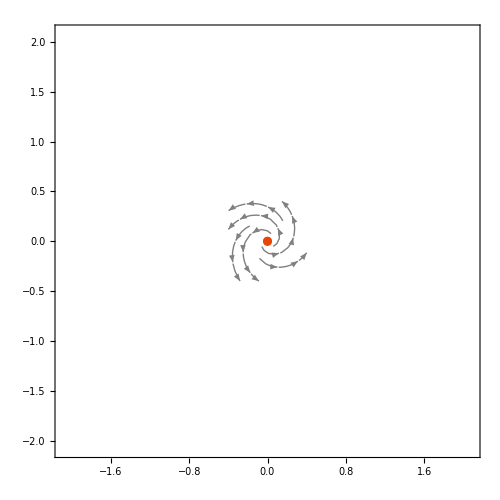

```mathematica
p1 := StreamPlot[{f,g},{x,-2,2},{y,-2,2},ImageSize->500,StreamStyle->Gray,StreamPoints->70,StreamScale->0.05,RegionFunction->Function[{x,y,vx,vy,n},x^10+y^10<(.4)^10]];
p3:=ListPlot[{{0,0}},PlotStyle->ColorData["SolarColors"][.4]];
Show[p1,p3]
```

### Away from the equilibrium point

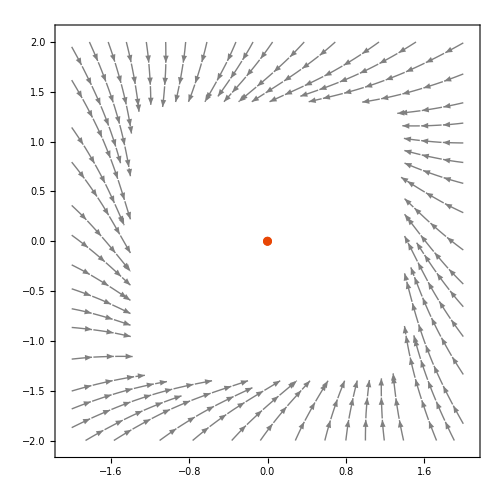

```mathematica
p1 := StreamPlot[{f,g},{x,-2,2},{y,-2,2},ImageSize->500,StreamStyle->Gray,StreamPoints->60,StreamScale->0.05,RegionFunction->Function[{x,y,vx,vy,n},x^10+y^10>1.4^10]];
p2 := ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->ColorData["SolarColors"][.8]];
p3:=ListPlot[{{0,0}},PlotStyle->ColorData["SolarColors"][.4]];
Show[p1,p3]
```

### Viewing Everything

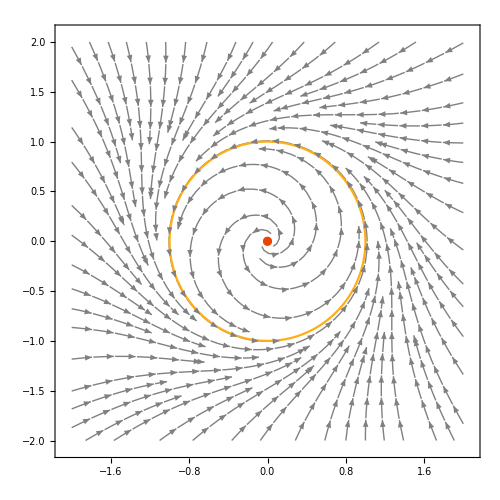

```mathematica
p1 := StreamPlot[{f,g},{x,-2,2},{y,-2,2},ImageSize->500,StreamStyle->Gray,StreamPoints->60,StreamScale->0.05];
p2 := ParametricPlot[{Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->ColorData["SolarColors"][.8]];
p3:=ListPlot[{{0,0}},PlotStyle->ColorData["SolarColors"][.4]];
Show[p1,p2,p3]
```